```mathematica
双直导线截面上的磁力线分布——参数方程法
```

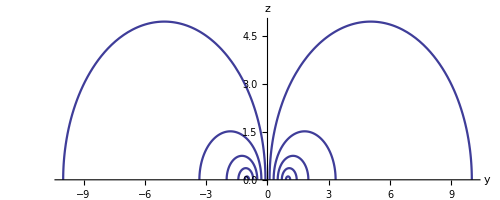

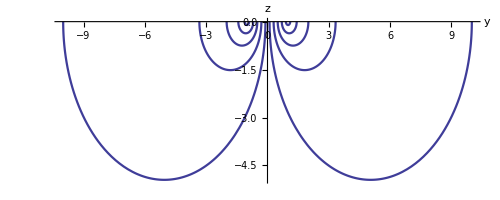

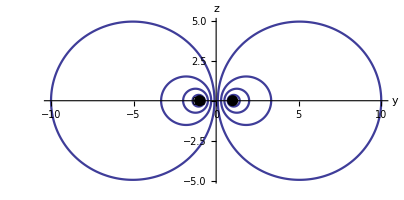

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
By[y_,z_]:=(1/((d/2-y)^2+z^2)-1/((d/2+y)^2+z^2)) z;
Bz[y_,z_]:=(d/2-y)/((d/2-y)^2+z^2)+(d/2+y)/((d/2+y)^2+z^2);
d=2;r=10.0^-3;z0=0;
(*................................*)
forceline={};
equ1={y'[ξ]==By[y[ξ],z[ξ]],z'[ξ]==Bz[y[ξ],z[ξ]],
y[0]==y0,z[0]==z0};
Do[
s=NDSolve[equ1,{y,z},{ξ,0,∞},MaxSteps->∞,
Method->{"EventLocator","Event"->z[ξ]<-r}];
{y,z}={y,z}/.s[[1]];
end =
 InterpolatingFunctionDomain[First[y/.s]][[1,-1]];
fig=ParametricPlot[{y[ξ],z[ξ]},{ξ,0,end},
PlotStyle->Thickness[0.004]];
AppendTo[forceline,fig];Clear[y,z],
{y0,-0.9d/2,0.9d/2,0.2d/2}]
g1=Show[forceline,PlotRange->All,
AxesStyle->Thickness[0.003],
AxesOrigin->{0,0},AxesLabel->{"y","z"}]
(*................................*)
forceline={};
equ2={y'[ξ]==-By[y[ξ],z[ξ]],z'[ξ]==-Bz[y[ξ],z[ξ]],
y[0]==y0,z[0]==z0};
Do[
s=NDSolve[equ2,{y,z},{ξ,0,∞},MaxSteps->∞,
Method->{"EventLocator","Event"->z[ξ]>r}];
{y,z}={y,z}/.s[[1]];
end =
 InterpolatingFunctionDomain[First[y/.s]][[1,-1]];
fig=ParametricPlot[{y[ξ],z[ξ]},{ξ,0,end},
PlotStyle->Thickness[0.004]];
AppendTo[forceline,fig];Clear[y,z],
{y0,-0.9d/2,0.9d/2,0.2d/2}]
g2=Show[forceline,PlotRange->All,
AxesStyle->Thickness[0.003],
AxesOrigin->{0,0},AxesLabel->{"y","z"}]
(*................................*)
Show[{g1,g2},AxesOrigin->{0,0},
AxesStyle->Thickness[0.003],PlotRange->All,
Epilog->{PointSize[0.02],
Point/@{{-d/2,0},{d/2,0}}}]
Clear[Bz,By,y,z]
```